```mathematica
μ = Sqrt[δ^2 + 4^2];
```

```mathematica
envel2 = (4*4^2/μ^2)*Sin[μ*τ/2]^2*(Cos[μ*τ/2]Cos[δ*τ/2]+(δ/μ)Sin[μ*τ/2]Sin[δ*τ/2])^2;
```

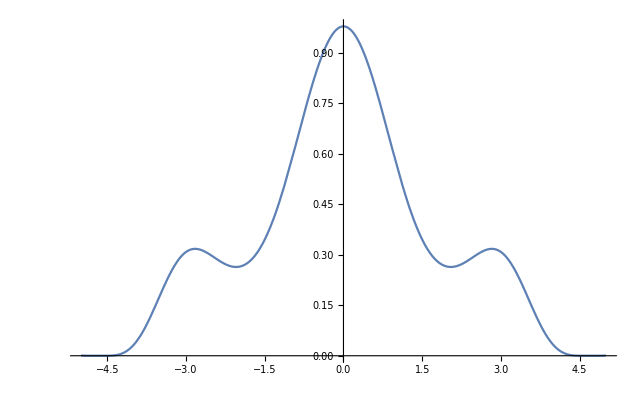

```mathematica
p1 = Plot[envel2/.τ->2, {δ,-5,5}, PlotRange -> All]
```

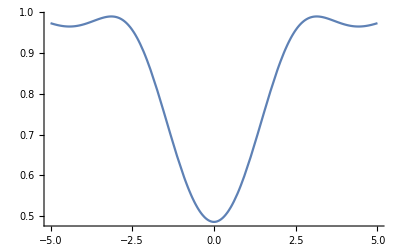

```mathematica
p2 = Plot[(Cos[μ*τ/2]Cos[δ*τ/2]+(δ/μ)Sin[μ*τ/2]Sin[δ*τ/2])^2/.τ-> 2,{δ,-5,5}, PlotRange -> All]
```

```mathematica
fringe = (4*3.415^2/μ^2)*Sin[μ*τ/2]^2*(Cos[μ*τ/2]Cos[δ*T/2]+(δ/μ)Sin[μ*τ/2]Sin[δ*T/2])^2;
```

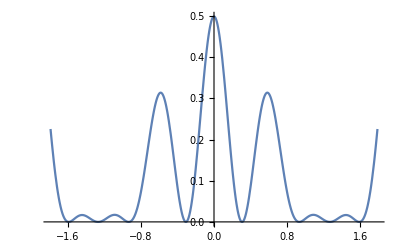

```mathematica
p3 = Plot[fringe /. {τ-> 3.45, T -> 10}, {δ,-1.788,1.788}, PlotRange -> All]
```

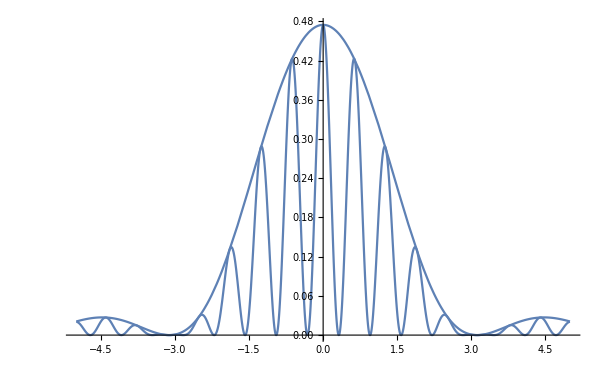

```mathematica
Show[p1,p3]
```

```mathematica
Manipulate[Plot[(4*Rabi^2/((12*2*Pi*(δ+Δ-center))^2 + Rabi^2))*Sin[Sqrt[(12*2*Pi*(δ+Δ-center))^2 + Rabi^2]*τ/2]^2*(Cos[Sqrt[(12*2*Pi*(δ+Δ-center))^2 + Rabi^2]*τ/2]Cos[(12*2*Pi*(δ-center))*T/2]-((12*2*Pi*(δ+Δ-center))/Sqrt[(12*2*Pi*(δ+Δ-center))^2 + Rabi^2])Sin[Sqrt[(12*2*Pi*(δ+Δ-center))^2 + Rabi^2]*τ/2]Sin[(12*2*Pi*(δ-center))*T/2])^2  /. center -> 0.3745,{δ,0.3,0.45}, PlotRange -> {{0.3,0.45},{0,1}}],{τ,0.001,200},{T,0.001,200}, {Rabi,0.001,10}, {Δ, -10, 10}]
```

```mathematica
Manipulate[Plot[(4*Rabi^2/((12*2*Pi*(Δo+Δ))^2 + Rabi^2))*Sin[Sqrt[(12*2*Pi*(Δo+Δ))^2 + Rabi^2]*τ/2]^2*(Cos[Sqrt[(12*2*Pi*(Δo+Δ))^2 + Rabi^2]*τ/2]Cos[(12*2*Pi*(Δo))*T/2]-((12*2*Pi*(Δo+Δ))/Sqrt[(12*2*Pi*(Δo+Δ))^2 + Rabi^2])Sin[Sqrt[(12*2*Pi*(Δo+Δ))^2 + Rabi^2]*τ/2]Sin[(12*2*Pi*(Δo))*T/2])^2 ,{T, 0, 20}, PlotRange -> {{0,20},{0,1}}],{τ,0.001,200},{Δo, -0.1, 0.1}, {Rabi,-0.5,0.5}, {Δ, -0.02, 0.02}]
```

```mathematica
Manipulate[Plot[(Cos[(12*2*Pi*(Δo))*T/2])^2 ,{T, 0, 20}, PlotRange -> {{0,20},{0,1}}],{Δo, -0.1, 0.1}]
```